# Numeric evolution of a quantum state

Evolve a quantum state in time, numerically

## Example Content

In the Wolfram quantum framework, quantum objects and operations can be defined symbolically and also numerically. In this regard, time evolution of quantum system can be treated symbolically and also numerically.

Install and load the QuantumFramework paclet:

```mathematica
PacletInstall["Wolfram/QuantumFramework"]
Needs["Wolfram`QuantumFramework`"]
```

Given a time-independent Hamiltonian as 0.2 σ_x+0.8 σ_y, find the quantum state at the later time, with ψ_0=0:

```mathematica
ψf=QuantumEvolve[QuantumOperator[.2"X"+.8"Y"],{t,0,3}]
```

QuantumState[…]

Visualize the trajectory in Bloch sphere:

```mathematica
ListAnimate[Table[ψf[t]["BlochPlot"],{t,0,3,.1}]]
```

Given a time-dependent Hamiltonian as cos(0.2t)σ_x+sin(0.8t)σ_y, find the quantum state at the later time, with ψ_0=0:

```mathematica
ψf=QuantumEvolve[Cos[.2 t]QuantumOperator["X"]+Sin[.8 t]QuantumOperator["Y"],{t,0,10}]
```

QuantumState[…]

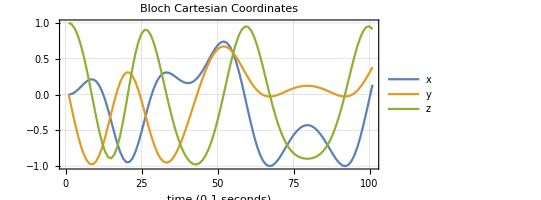

```mathematica
ListPlot[Transpose[Table[ψf[t]["BlochCartesianCoordinates"],{t,0,10,.1}]],Joined->True,PlotLegends->{"x","y","z"},PlotLabel->"Bloch Cartesian Coordinates",GridLines->Automatic,FrameLabel->{"time (0.1 seconds)",None},Frame->True,AspectRatio->1/2]
```

## Supporting Data and Definitions

(Your data can be Dataset[…], EntityStore[…], Image[…], Audio[…] or any other expression)

```mathematica
ResourceData[{{}},"NameOfContent"]=xxxx
```

(xxxx can be your data, or File[…], CloudObject[…] or LocalObject[…] that contains it.)

## Thumbnail Image

-Graphics-

## Source & Additional Information

### Contributed By

Wolfram Research, Quantum Computation Framework Team

### Keywords

keyword 1

### Categories

Algebra
 Calculus
 Complex Systems
 Control Systems
 Engineering
 Food & Nutrition
 Graphs & Networks
 Machine Learning
 Optimization
 Puzzles and Recreation
 System Modeling
 Video Processing
  |  Astronomy
 Cellular Automata
 Computer Science
 Creative Arts
 Finance & Economics
 Geography
 Image Processing
 Mathematics
 Physics
 Signal Processing
 Text & Language Processing
 Visualization & Graphics
 |  Audio Processing
 Chemistry
 Computer Vision
 Data Science
 Finite Element Method
 Geometry
 Life Sciences
 Notebooks & User Interfaces
 Presentation & Publication
 Social Sciences
 Time-Related Computation
 Quantum Computation

### Related Documentation Pages

Symbol name or documentation URI

### Related Resource Objects

Resource Name (resources from any Wolfram repository)

### Original Source References and Attributions

Source, reference or citation

### Links

https://resources.wolframcloud.com/PacletRepository/resources/Wolfram/QuantumFramework/

### Compatibility

#### Wolfram Language Version

13.2+

#### Operating System

Windows |  Mac |  Linux

#### Environments

SessionLocal or cloud interactive session
 WebEvaluationCloud evaluation initiated by an HTTP request
 BatchJobRemote batch job |  ScriptScript run in batch mode
 WebAPIAPI called through an HTTP request
 |  SubkernelParallel or grid subkernel
 ScheduledScheduled task

#### Cloud Support

Supported in cloud

#### Required Features

Notebooks |  Parallel Kernels |  Cloud Access

## Author Notes

Additional information about limitations, issues, etc.